```mathematica
Off[LinearSolve::luc]
Off[$RecursionLimit::reclim2]
colo=ColorData[3,"ColorList"][[{6,2,4}]]
```

{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]}

1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
MUL=1;
pi="-";

LITham[hh_,nn_,σr_,σi_,B0_]:=Det[hh-(B0+σr+I σi) nn];

LofM[jjJ_,mmJ_,sR_,sI_]:=Module[{mJ=mmJ,jJ=jjJ,sigmaRange=sR,sigmaI=sI},
momentum=1;
file="~/kette_repo/ComptonLIT/av18_deuteron/norm-ham-litME-"<>ToString[jJ]<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="~/kette_repo/ComptonLIT/av18_deuteron/LIT_SOURCE_"<>ToString[jJ]<>pi<>ToString[mJ]<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
Dimensions[norm];Dimensions[ham];
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[momentum]];
litOfSigma={};
psilitOfSigma={};
For[n=1,n<=nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
psilitOfSigma=Append[psilitOfSigma,coeff];
litOfSigma=Append[litOfSigma,4 Pi/(2 jJ+1) Conjugate[coeff].norm.coeff];
)];

{litOfSigma,norm,ham,psilitOfSigma}
]
```

Setup of the RHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_deu-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_deu]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

$Aborted

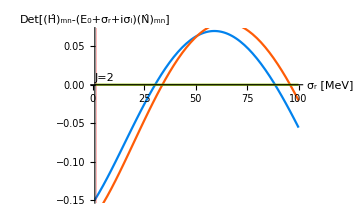
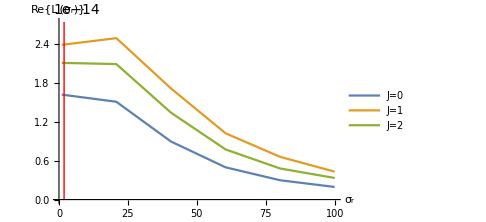
-Graphics- | -Graphics-E_0 = -1.8556 MeV

```mathematica
j0=0;jmax=2;
σI=32;
smin=1;smax=100;nbrs=6;
σR=Range[smin,smax,(smax-smin)/(nbrs-1)];
Export["sRange",{σI,N[σR]},"Table","FieldSeparators"->" ; "];

Lit={};
Mats={};
For[jj=j0,jj≤jmax,jj++,(
For[mmj=-jj,mmj≤jj,mmj++,(
coflis=LofM[jj,mmj,σR,σI][[4]]//Flatten;
coflist=Transpose[{Re[coflis],Im[coflis]}];
Export["COEFFS_LIT_J"<>ToString[jj]<>"mJ"<>ToString[mmj],coflist,"Table","FieldSeparators"->" ; "];
)];

Mats=Append[Mats,{LofM[jj,0,σR,σI][[2]],LofM[jj,0,σR,σI][[3]]}];
Ltmp= Sum[Table[Re[LofM[jj,m,σR,σI][[1]]],{m,-jj,jj}][[i]],{i,1,2 jj+1}];
Lit=Append[Lit,Transpose[{σR,Ltmp}]];
)]
Abort[];
file="~/kette_repo/ComptonLIT/av18_deuteron/E0.dat";
Ed=Read[file];Close[file];

Labeled[
Grid[{{
Show[Table[Plot[Re[LITham[Mats[[j]][[2]],Mats[[j]][[1]],sr,σI,Ed]],{sr,smin,smax},PlotLabels->Placed["J="<>ToString[j-1],Above],AxesLabel->{"σ_r [MeV]","Det[(Ĥ)_mn-(E_0+σ_r+iσ_i)(N̂)_mn]"},
ImageSize->Medium,GridLines->{{{-Ed,Red}},None},PlotStyle->{colo[[j]]}],{j,1,1+jmax-j0}]]
,
ListLinePlot[Lit,
PlotLegends->Placed[{"J=0","J=1","J=2"},Above],AxesLabel->{"σ_r","Re{L_j(σ_r)}"},PlotRange->{0,1.1 Max[Lit[[2]][[All,2]]]},
ImageSize->Medium,
Epilog->{Directive[{Red}],Line[{{-Ed,0},{-Ed,1.1 Max[Lit[[2]][[All,2]]]}}]}]
}}
],{"E_0 = "<>ToString[Ed]<>" MeV"},{Top}]
```